busSimulation[size, time] returns a simulation of times steps and size 5w×size .

```mathematica
busSimulation[size_,time_]:=Module[{track,t=0,base},
track=Table[0,{2},{size 5  w+vmax-am}];
base=ConstantArray[0,w+vmax-am];
(*put statios*)
track[[1]]=stations[];
(*put lights*)
track[[1]]=lights[1/5];
(*fill with test stuff*)
track[[2]][[1;;5]]={{0,0},{0,0},{0,0},{0,0},{7,0,0}};
track[[2]][[1;;5]]={{4,0},{3,0},{2,0},{1,0},{7,0,0}}(*bus ahead, going fast, brake*);
track[[2]][[10;;14]]={{4,0},{3,0},{2,0},{1,0},{7,0,0}}(*bus ahead, going fast, brake*);
track[[2]][[20;;23]]=track[[2]][[1;;4]];
track[[2]][[24]]={0,0,0}(*bus ahead, stoped, wait*);
track[[2]][[25;;28]]=track[[2]][[1;;4]];
track[[2]][[29]]={7,0,0}(*bus ahead, going fast, brake*);
track[[2]][[95;;98]]=track[[2]][[1;;4]];
track[[2]][[99]]={4,0,0}(*light ahead with bus before light*); 
track[[2]][[37;;40]]=track[[2]][[1;;4]];
track[[2]][[41]]={3,0,0}(*station ahead with bus before station, hold*); 
track[[2]][[60;;63]]=track[[2]][[1;;4]];
track[[2]][[64]]={0,0,0}(*accelerate, nothing nearby*);
track[[2]][[100;;103]]=track[[2]][[1;;4]];
track[[2]][[104]]={6,0,0}(*light behind*);
track[[2]][[50;;53]]=track[[2]][[1;;4]];
track[[2]][[54]]={0,0,0}(*bus at a station, all wagons are idle, move*);
track[[2]][[150;;153]]=track[[2]][[1;;4]];
track[[2]][[154]]={4,0,0}(*bus at a station, brake, change status*);
track[[2]][[247;;250]]=track[[2]][[1;;4]];
track[[2]][[251]]={4,0,0}(*station ahead, fast, brake*);
track[[2]][[344;;347]]=track[[2]][[1;;4]];
track[[2]][[348]]={6,0,0}(*station ahead, brake*);
track[[2]][[450;;453]]=track[[2]][[1;;4]];
track[[2]][[454]]={3,0,0}(*station ahead, fast brake*);
track[[2]][[548;;551]]=track[[2]][[1;;4]];
track[[2]][[552]]={1,0,0}(*station ahead, close, slow, accelerate*);
track[[2]][[648;;651]]=track[[2]][[1;;4]];
track[[2]][[652]]={6,0,0}(*station ahead, close, fast, brake*);
track[[2]][[750;;753]]=track[[2]][[1;;4]]/.{d_,0}:>{d,p/2};
track[[2]][[754]]={0,1,p/2}(*bus at a station unloading, unload and change status to load*);
track[[1]][[850]]={0,100,62};
track[[1]][[851]]={10,100,46};
track[[1]][[852]]={50,100,74};
track[[1]][[853]]={70,100,84};
track[[1]][[854]]={100,100,62};
track[[2]][[850;;853]]=track[[2]][[1;;4]]/.{d_,0}:>{d,p/2};
track[[2]][[854]]={0,2,0}(*bus at a station loading, load and change status to idle*);
track[[2]][[196;;199]]=track[[2]][[1;;4]];
track[[2]][[200]]={3,0,0}(*red light, bus head at light, bus moving, stop*);
track[[2]][[296;;299]]=track[[2]][[1;;4]];
track[[2]][[300]]={0,0,0}(*red light, bus head at light, bus stoped, wait*);
track[[1,400,2]]=0; 
track[[2]][[396;;399]]=track[[2]][[1;;4]];
track[[2]][[400]]={5,0,0}(*Red light, bus head at light, bus moving fast, move*);
track[[1,500,1,2]]=1; 
track[[2]][[491;;494]]=track[[2]][[1;;4]];
track[[2]][[495]]={4,0,0}(*green light, move*); 
track[[2]][[590;;593]]=track[[2]][[1;;4]];
track[[2]][[594]]={4,0,0}(*red light, far, fast, hold*);
track[[2]][[694;;697]]=track[[2]][[1;;4]];
track[[2]][[698]]={2,0,0}(*red light, close, slow,hold*);
(*run the sim*)
NestList[advanceOne,track,time]
]
```

```mathematica
updated=advanceOne[track];
```

```mathematica
heads=Position[track[[2]],{_,_,_}]//Flatten;
neighbors={track[[1]][[#-w;;#+vmax-am-1]],track[[2]][[#-w;;#+vmax-am-1]]}&/@heads;
```

```mathematica
bn=1;
neighbors[[bn]]//MatrixForm
move[neighbors[[bn]]]//MatrixForm
{updated[[1]][[#-w;;#+vmax-am-1]],updated[[2]][[#-w;;#+vmax-am-1]]}&[heads[[bn]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{4,0} | {3,0} | {2,0} | {1,0} | {7,0,0} | 0 | 0 | 0 | 0 | {4,0} | {3,0} | {2,0} | {1,0} | {7,0,0} | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | {4,0} | {3,0} | {2,0} | {1,0} | {4,0,0} | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | {4,0} | {3,0} | {2,0} | {1,0} | {4,0,0} | 0 | 0 | 0 | 0 | {4,0} | {3,0})

```mathematica
updated2=advanceOne[updated];
```

```mathematica
heads=Position[updated[[2]],{_,_,_}]//Flatten;
neighbors={updated[[1]][[#-w;;#+vmax-am-1]],updated[[2]][[#-w;;#+vmax-am-1]]}&/@heads;
```

```mathematica
Length[heads]
```

24

```mathematica
bn=5;
neighbors[[bn]]//MatrixForm
move[neighbors[[bn]]]//MatrixForm
{updated2[[1]][[#-w;;#+vmax-am-1]],updated2[[2]][[#-w;;#+vmax-am-1]]}&[heads[[bn]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | {100,100,92} | {20,100,4} | {100,100,58} | {90,100,18} | {100,100,54} | 0 | 0 | 0 | 0 | 0
{4,0} | {3,0} | {2,0} | {1,0} | {4,0,0} | {4,0} | {3,0} | {2,0} | {1,0} | {0,1,0} | 0 | 0 | 0 | 0 | 0)

Station

station way ahead or behind or bus before station

Bus ahead, moving

{{4,0,0},0}

Set speed

{{4,0,0},{1},0,False,False,False}

(0 | 0 | 0 | 0 | 0 | {100,100,92} | {20,100,4} | {100,100,58} | {90,100,18} | {100,100,54} | 0 | 0 | 0 | 0 | 0
{4,0} | {3,0} | {2,0} | {1,0} | {0,0,0} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | {100,100,92} | {24,100,4} | {100,100,58} | {100,100,18} | {100,100,54} | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | {4,0} | {3,0} | {2,0} | {1,0} | {0,2,0} | 0 | 0 | 0 | 0 | 0)

```mathematica
track=updated;
updated=updated2;
```

```mathematica
data=busSimulation[100,100];
```

```mathematica
data[[1]]
```

```mathematica
Raster
```

```mathematica
White//FullForm
```

GrayLevel[1]

```mathematica
colorRulesUp={0->White,{pi_,pt_,_}:>Opacity[(pi+1)/(pt+1),Purple],{{ω_,ϕ_},t_}:>Piecewise[{{Green,Sin[ω t+ϕ]>0},{Red,Sin[ω t+ϕ]≤ 0},{Black,True}}]};
```

```mathematica
colorRulesDown={0->GrayLevel[.8],{_,_}->Blue,{_,_,_}->Blue};
```

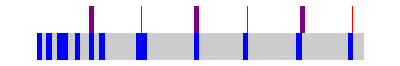

```mathematica
ArrayPlot[{data[[1]][[1]][[1;;310]]/.colorRulesUp,data[[1]][[2]][[1;;310]]/.colorRulesDown},AspectRatio->1/6]
```

```mathematica
ArrayPlot[{#[[1]][[280;;610]]/.colorRulesUp,#[[2]][[280;;610]]/.colorRulesDown},AspectRatio->1/4]&/@data;
```

```mathematica
ListAnimate[%]
```

```mathematica
Export["/home/jovillal/Downloads/buses.gif",%311]
```

/home/jovillal/Downloads/buses.gif

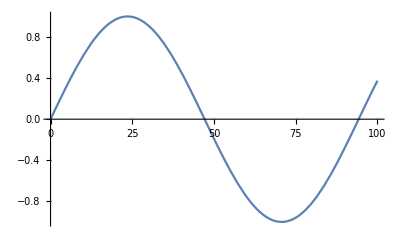

```mathematica
Plot[Sin[ t/15],{t,0,100}]
```

```mathematica
Length[base]-w-1
```

10

```mathematica
i=68;
heads=Position[data[[i,2]],{_,_,_}]//Flatten;
neighbors={data[[i,1]][[#-w;;#+vmax-am-1]],data[[i,2]][[#-w;;#+vmax-am-1]]}&/@heads;
```

```mathematica
Length[neighbors]
```

40

```mathematica
bn=7;
neighbors[[bn]]//MatrixForm
move[neighbors[[bn]]]//MatrixForm
(*{data[[i+1,1]][[#-w;;#+vmax-am-1]],data[[i+1,2]][[#-w;;#+vmax-am-1]]}&[heads[[bn]]]//MatrixForm*)
```

({100,100,92} | {100,100,79} | {100,100,21} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{4,0} | {3,0} | {2,0} | {1,0} | {2,0,0} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {4,0})

({100,100,92} | {100,100,79} | {100,100,21} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | {4,0} | {3,0} | {2,0} | {1,0} | {4,0,0} | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
test[{top:{___,s_List/;Length[s]==3,___},bottom:{wagons:__,h:{v_,_,_},___,{_,_},___}}]:={Position[top,_List,1][[-1,1]],Position[bottom[[w+2;;-1]],_List,1][[1,1]]+w+1}
```

```mathematica
move[neighbors[[bn]]]
```

{{0,0,0,0,0,{100,100,85},{100,100,63},{96,100,48},{100,100,99},{100,100,85},0,0,0,0,0},{0,0,0,0,{4,0},{3,0},{2,0},{1,0},{4,0,0},0,0,0,0,0,0}}

```mathematica
Flatten[{Table[i->neighbors[[bn]][[2]][[i]],{i,w}],w+1->{0,h2,h3}},1]
```

{1→{4,0},2→{3,0},3→{2,0},4→{1,0},5→{0,h2,h3}}

```mathematica
neighbors[[bn]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | {7,100,7} | {70,100,70} | {9,100,9} | {2,100,2} | {37,100,37} | 0 | 0 | 0 | 0 | 0
{4,0} | {3,0} | {2,0} | {1,0} | {0,0,0} | {4,56} | {3,100} | {2,72} | {1,16} | {0,0,100} | 0 | 0 | 0 | 0 | 0)

```mathematica
Count[neighbors[[bn]][[2]][[w+2;;-3]],_List]
```

0

```mathematica
neighbors[[bn]][[2]][[w+2;;-1]]
```

{0,0,0,0,0,0,0,0,{4,0},{3,0}}

```mathematica
Clear[test]
```

```mathematica
test[{top:{___,s_List/;Length[s]==3,___},bottom:{wagons:__,h:{v_,_,_},rest__}}]:={Count[top,_List],Position[top,{_,_,_}][[-1,1]],Position[{rest},_List,1,1][[1,1]]+w+1}
```

```mathematica
test[neighbors[[6]]]
```

{5,5,11}

```mathematica
neighbors[[6]]
```

{{{0,100,3},{0,100,67},{0,100,46},{0,100,60},{0,100,37},0,0,0,0,0,0,0,0,0,0},{{4,0},{3,0},{2,0},{1,0},{0,0,0},0,0,0,0,0,{4,0},{3,0},{2,0},{1,0},{0,0,0}}}

```mathematica
Count[neighbors[[6,2]],0]==Length[base]-w-1
```

True